```mathematica
Rho1s=300;
C1s=1377;
k1s=0.082;
Rho2s=862;
C2s=2100;
k2s=0.37;
Rho3s=74.2;
C3s=1726;
k3s=0.045;
Rho4s=1.18;
C4s=1005;
k4s=0.028;
ks1=20;
ks2=9.5;
a1s=k1s/(C1s*Rho1s);
a2s=k2s/(C2s*Rho2s);
a3s=k3s/(C3s*Rho3s);
a4s=k4s/(C4s*Rho4s);
x1s=0.0006;x2s=0.006;x3s=0.0036;x4s=0.005;ts=1700;
```

```mathematica
Sol=Table[0,{i,1,109},{j,1,170001}];
For[cnt=1,cnt≤170001,cnt++,Sol[[1]][[cnt]]=75;Sol[[109]][[cnt]]=37
]
For[cnt=2,cnt≤109,cnt++,Sol[[cnt]][[1]]=37
]
```

```mathematica
dy=0.01;dx1=0.0001;dx2=0.0001;dx3=0.0001;dx4=0.001;
sigma1=a1s*dy/(dx1*dx1);sigma2=a2s*dy/(dx2*dx2);sigma3=a3s*dy/(dx3*dx3);sigma4=a4s*dy/(dx4*dx4);
```

```mathematica
For[j=2,j≤170001,j++,
{
For[i=2,i≤6,i++,
Sol[[i]][[j]]=sigma1*Sol[[i+1]][[j-1]]+sigma1*Sol[[i-1]][[j-1]]-(2*sigma1-1)*Sol[[i]][[j-1]]
];
For[i=8,i≤66,i++,
Sol[[i]][[j]]=sigma2*Sol[[i+1]][[j-1]]+sigma2*Sol[[i-1]][[j-1]]-(2*sigma2-1)*Sol[[i]][[j-1]]
];
For[i=68,i≤102,i++,
Sol[[i]][[j]]=sigma3*Sol[[i+1]][[j-1]]+sigma3*Sol[[i-1]][[j-1]]-(2*sigma3-1)*Sol[[i]][[j-1]]
];
For[i=104,i≤107,i++,
Sol[[i]][[j]]=sigma4*Sol[[i+1]][[j-1]]+sigma4*Sol[[i-1]][[j-1]]-(2*sigma4-1)*Sol[[i]][[j-1]]
];
Sol[[7]][[j]]=(Sol[[8]][[j]]-Sol[[6]][[j]])/(k1s/dx1+k2s/dx2)*k2s/dx2+Sol[[6]][[j]];
Sol[[67]][[j]]=(Sol[[68]][[j]]-Sol[[66]][[j]])/(k2s/dx2+k3s/dx3)*k3s/dx3+Sol[[66]][[j]];
Sol[[103]][[j]]=(Sol[[104]][[j]]-Sol[[102]][[j]])/(k3s/dx3+ks1)*ks1+Sol[[102]][[j]];
Sol[[108]][[j]]=(Sol[[109]][[j]]-Sol[[107]][[j]])/(k4s/dx4+ks2)*ks2+Sol[[107]][[j]]
}
]
```

```mathematica
mesh=Table[Sol[[i]][[100*j+1]],{i,1,109},{j,0,1700}];
```

```mathematica
data=Import["D:\\Mod\\temperature.xlsx"];
```

```mathematica
actual=Table[data[[1]][[i]][[2]],{i,3,1703}];
```

```mathematica
mesh[[108]]
```

{37,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.0001,37.0002,37.0005,37.001,37.0019,37.0034,37.0055,37.0084,37.0123,37.0174,37.0238,37.0315,37.0409,37.0518,37.0645,37.0789,37.0951,37.1132,37.1332,37.155,37.1786,37.2041,37.2314,37.2605,37.2913,37.3239,37.358,37.3937,37.4309,37.4696,37.5097,37.5511,37.5938,37.6376,37.6826,37.7287,37.7758,37.8238,37.8728,37.9225,37.9731,38.0243,38.0763,38.1288,38.1819,38.2355,38.2896,38.3441,38.399,38.4543,38.5098,38.5656,38.6216,38.6779,38.7343,38.7908,38.8475,38.9042,38.961,39.0178,39.0746,39.1314,39.1882,39.2449,39.3016,39.3581,39.4146,39.4709,39.5271,39.5831,39.639,39.6947,39.7503,39.8056,39.8607,39.9156,39.9703,40.0248,40.079,40.133,40.1867,40.2402,40.2935,40.3464,40.3991,40.4515,40.5037,40.5556,40.6072,40.6585,40.7095,40.7602,40.8107,40.8608,40.9107,40.9602,41.0095,41.0585,41.1071,41.1555,41.2036,41.2514,41.2989,41.346,41.3929,41.4395,41.4858,41.5318,41.5775,41.6229,41.668,41.7129,41.7574,41.8016,41.8456,41.8892,41.9326,41.9757,42.0185,42.061,42.1032,42.1451,42.1868,42.2282,42.2693,42.3101,42.3507,42.391,42.431,42.4707,42.5102,42.5494,42.5883,42.627,42.6654,42.7035,42.7414,42.779,42.8164,42.8535,42.8903,42.9269,42.9633,42.9994,43.0353,43.0709,43.1062,43.1414,43.1762,43.2109,43.2453,43.2795,43.3134,43.3471,43.3805,43.4138,43.4468,43.4796,43.5121,43.5444,43.5765,43.6084,43.6401,43.6715,43.7028,43.7338,43.7646,43.7952,43.8255,43.8557,43.8856,43.9154,43.9449,43.9743,44.0034,44.0323,44.0611,44.0896,44.1179,44.1461,44.174,44.2018,44.2293,44.2567,44.2839,44.3109,44.3377,44.3643,44.3907,44.417,44.4431,44.4689,44.4947,44.5202,44.5455,44.5707,44.5957,44.6206,44.6452,44.6697,44.694,44.7182,44.7422,44.766,44.7896,44.8131,44.8365,44.8596,44.8826,44.9055,44.9282,44.9507,44.9731,44.9953,45.0174,45.0393,45.061,45.0826,45.1041,45.1254,45.1466,45.1676,45.1885,45.2092,45.2298,45.2502,45.2705,45.2907,45.3107,45.3306,45.3503,45.3699,45.3894,45.4087,45.4279,45.447,45.4659,45.4847,45.5034,45.5219,45.5404,45.5586,45.5768,45.5948,45.6128,45.6305,45.6482,45.6657,45.6832,45.7005,45.7176,45.7347,45.7516,45.7685,45.7852,45.8018,45.8183,45.8346,45.8509,45.867,45.883,45.8989,45.9147,45.9304,45.946,45.9615,45.9769,45.9921,46.0073,46.0223,46.0373,46.0521,46.0669,46.0815,46.0961,46.1105,46.1248,46.1391,46.1532,46.1673,46.1812,46.1951,46.2088,46.2225,46.236,46.2495,46.2629,46.2762,46.2893,46.3024,46.3155,46.3284,46.3412,46.3539,46.3666,46.3792,46.3916,46.404,46.4163,46.4285,46.4407,46.4527,46.4647,46.4766,46.4884,46.5001,46.5117,46.5233,46.5348,46.5462,46.5575,46.5687,46.5799,46.591,46.602,46.6129,46.6238,46.6346,46.6453,46.6559,46.6665,46.677,46.6874,46.6977,46.708,46.7182,46.7283,46.7384,46.7483,46.7583,46.7681,46.7779,46.7876,46.7973,46.8068,46.8164,46.8258,46.8352,46.8445,46.8538,46.8629,46.8721,46.8811,46.8901,46.8991,46.9079,46.9167,46.9255,46.9342,46.9428,46.9514,46.9599,46.9684,46.9768,46.9851,46.9934,47.0016,47.0098,47.0179,47.0259,47.0339,47.0418,47.0497,47.0576,47.0653,47.0731,47.0807,47.0883,47.0959,47.1034,47.1109,47.1183,47.1256,47.1329,47.1402,47.1474,47.1546,47.1617,47.1687,47.1757,47.1827,47.1896,47.1964,47.2033,47.21,47.2167,47.2234,47.23,47.2366,47.2432,47.2497,47.2561,47.2625,47.2689,47.2752,47.2814,47.2877,47.2938,47.3,47.3061,47.3121,47.3181,47.3241,47.33,47.3359,47.3418,47.3476,47.3534,47.3591,47.3648,47.3704,47.376,47.3816,47.3871,47.3926,47.3981,47.4035,47.4089,47.4142,47.4195,47.4248,47.43,47.4352,47.4404,47.4455,47.4506,47.4556,47.4607,47.4656,47.4706,47.4755,47.4804,47.4852,47.49,47.4948,47.4996,47.5043,47.509,47.5136,47.5182,47.5228,47.5274,47.5319,47.5364,47.5408,47.5453,47.5497,47.554,47.5584,47.5627,47.5669,47.5712,47.5754,47.5796,47.5837,47.5879,47.592,47.5961,47.6001,47.6041,47.6081,47.6121,47.616,47.6199,47.6238,47.6276,47.6315,47.6353,47.639,47.6428,47.6465,47.6502,47.6539,47.6575,47.6611,47.6647,47.6683,47.6718,47.6754,47.6789,47.6823,47.6858,47.6892,47.6926,47.696,47.6993,47.7027,47.706,47.7092,47.7125,47.7157,47.719,47.7222,47.7253,47.7285,47.7316,47.7347,47.7378,47.7409,47.7439,47.7469,47.7499,47.7529,47.7559,47.7588,47.7617,47.7646,47.7675,47.7703,47.7732,47.776,47.7788,47.7816,47.7843,47.7871,47.7898,47.7925,47.7952,47.7978,47.8005,47.8031,47.8057,47.8083,47.8109,47.8135,47.816,47.8185,47.821,47.8235,47.826,47.8284,47.8309,47.8333,47.8357,47.8381,47.8404,47.8428,47.8451,47.8474,47.8497,47.852,47.8543,47.8566,47.8588,47.861,47.8632,47.8654,47.8676,47.8698,47.8719,47.874,47.8762,47.8783,47.8804,47.8824,47.8845,47.8865,47.8886,47.8906,47.8926,47.8946,47.8966,47.8985,47.9005,47.9024,47.9043,47.9062,47.9081,47.91,47.9119,47.9137,47.9156,47.9174,47.9192,47.921,47.9228,47.9246,47.9264,47.9281,47.9299,47.9316,47.9333,47.935,47.9367,47.9384,47.9401,47.9418,47.9434,47.945,47.9467,47.9483,47.9499,47.9515,47.9531,47.9546,47.9562,47.9578,47.9593,47.9608,47.9623,47.9638,47.9653,47.9668,47.9683,47.9698,47.9712,47.9727,47.9741,47.9755,47.9769,47.9784,47.9797,47.9811,47.9825,47.9839,47.9852,47.9866,47.9879,47.9893,47.9906,47.9919,47.9932,47.9945,47.9958,47.997,47.9983,47.9996,48.0008,48.0021,48.0033,48.0045,48.0057,48.0069,48.0081,48.0093,48.0105,48.0117,48.0128,48.014,48.0151,48.0163,48.0174,48.0185,48.0197,48.0208,48.0219,48.023,48.0241,48.0251,48.0262,48.0273,48.0283,48.0294,48.0304,48.0315,48.0325,48.0335,48.0345,48.0355,48.0365,48.0375,48.0385,48.0395,48.0405,48.0414,48.0424,48.0433,48.0443,48.0452,48.0462,48.0471,48.048,48.0489,48.0498,48.0507,48.0516,48.0525,48.0534,48.0543,48.0551,48.056,48.0569,48.0577,48.0586,48.0594,48.0602,48.0611,48.0619,48.0627,48.0635,48.0643,48.0651,48.0659,48.0667,48.0675,48.0683,48.069,48.0698,48.0706,48.0713,48.0721,48.0728,48.0736,48.0743,48.075,48.0758,48.0765,48.0772,48.0779,48.0786,48.0793,48.08,48.0807,48.0814,48.0821,48.0827,48.0834,48.0841,48.0848,48.0854,48.0861,48.0867,48.0874,48.088,48.0886,48.0893,48.0899,48.0905,48.0911,48.0918,48.0924,48.093,48.0936,48.0942,48.0948,48.0954,48.0959,48.0965,48.0971,48.0977,48.0982,48.0988,48.0994,48.0999,48.1005,48.101,48.1016,48.1021,48.1027,48.1032,48.1037,48.1042,48.1048,48.1053,48.1058,48.1063,48.1068,48.1073,48.1078,48.1083,48.1088,48.1093,48.1098,48.1103,48.1108,48.1113,48.1117,48.1122,48.1127,48.1131,48.1136,48.1141,48.1145,48.115,48.1154,48.1159,48.1163,48.1167,48.1172,48.1176,48.1181,48.1185,48.1189,48.1193,48.1197,48.1202,48.1206,48.121,48.1214,48.1218,48.1222,48.1226,48.123,48.1234,48.1238,48.1242,48.1246,48.1249,48.1253,48.1257,48.1261,48.1264,48.1268,48.1272,48.1275,48.1279,48.1283,48.1286,48.129,48.1293,48.1297,48.13,48.1304,48.1307,48.1311,48.1314,48.1317,48.1321,48.1324,48.1327,48.1331,48.1334,48.1337,48.134,48.1343,48.1347,48.135,48.1353,48.1356,48.1359,48.1362,48.1365,48.1368,48.1371,48.1374,48.1377,48.138,48.1383,48.1386,48.1388,48.1391,48.1394,48.1397,48.14,48.1402,48.1405,48.1408,48.1411,48.1413,48.1416,48.1419,48.1421,48.1424,48.1426,48.1429,48.1432,48.1434,48.1437,48.1439,48.1442,48.1444,48.1447,48.1449,48.1451,48.1454,48.1456,48.1459,48.1461,48.1463,48.1466,48.1468,48.147,48.1472,48.1475,48.1477,48.1479,48.1481,48.1484,48.1486,48.1488,48.149,48.1492,48.1494,48.1496,48.1499,48.1501,48.1503,48.1505,48.1507,48.1509,48.1511,48.1513,48.1515,48.1517,48.1519,48.1521,48.1523,48.1524,48.1526,48.1528,48.153,48.1532,48.1534,48.1536,48.1537,48.1539,48.1541,48.1543,48.1545,48.1546,48.1548,48.155,48.1552,48.1553,48.1555,48.1557,48.1558,48.156,48.1562,48.1563,48.1565,48.1567,48.1568,48.157,48.1571,48.1573,48.1574,48.1576,48.1578,48.1579,48.1581,48.1582,48.1584,48.1585,48.1587,48.1588,48.159,48.1591,48.1592,48.1594,48.1595,48.1597,48.1598,48.1599,48.1601,48.1602,48.1604,48.1605,48.1606,48.1608,48.1609,48.161,48.1612,48.1613,48.1614,48.1615,48.1617,48.1618,48.1619,48.162,48.1622,48.1623,48.1624,48.1625,48.1626,48.1628,48.1629,48.163,48.1631,48.1632,48.1634,48.1635,48.1636,48.1637,48.1638,48.1639,48.164,48.1641,48.1642,48.1644,48.1645,48.1646,48.1647,48.1648,48.1649,48.165,48.1651,48.1652,48.1653,48.1654,48.1655,48.1656,48.1657,48.1658,48.1659,48.166,48.1661,48.1662,48.1663,48.1664,48.1665,48.1665,48.1666,48.1667,48.1668,48.1669,48.167,48.1671,48.1672,48.1673,48.1674,48.1674,48.1675,48.1676,48.1677,48.1678,48.1679,48.1679,48.168,48.1681,48.1682,48.1683,48.1684,48.1684,48.1685,48.1686,48.1687,48.1687,48.1688,48.1689,48.169,48.169,48.1691,48.1692,48.1693,48.1693,48.1694,48.1695,48.1696,48.1696,48.1697,48.1698,48.1698,48.1699,48.17,48.1701,48.1701,48.1702,48.1703,48.1703,48.1704,48.1705,48.1705,48.1706,48.1706,48.1707,48.1708,48.1708,48.1709,48.171,48.171,48.1711,48.1711,48.1712,48.1713,48.1713,48.1714,48.1714,48.1715,48.1716,48.1716,48.1717,48.1717,48.1718,48.1718,48.1719,48.1719,48.172,48.1721,48.1721,48.1722,48.1722,48.1723,48.1723,48.1724,48.1724,48.1725,48.1725,48.1726,48.1726,48.1727,48.1727,48.1728,48.1728,48.1729,48.1729,48.173,48.173,48.1731,48.1731,48.1732,48.1732,48.1733,48.1733,48.1733,48.1734,48.1734,48.1735,48.1735,48.1736,48.1736,48.1737,48.1737,48.1737,48.1738,48.1738,48.1739,48.1739,48.1739,48.174,48.174,48.1741,48.1741,48.1741,48.1742,48.1742,48.1743,48.1743,48.1743,48.1744,48.1744,48.1745,48.1745,48.1745,48.1746,48.1746,48.1746,48.1747,48.1747,48.1747,48.1748,48.1748,48.1749,48.1749,48.1749,48.175,48.175,48.175,48.1751,48.1751,48.1751,48.1752,48.1752,48.1752,48.1753,48.1753,48.1753,48.1753,48.1754,48.1754,48.1754,48.1755,48.1755,48.1755,48.1756,48.1756,48.1756,48.1756,48.1757,48.1757,48.1757,48.1758,48.1758,48.1758,48.1758,48.1759,48.1759,48.1759,48.176,48.176,48.176,48.176,48.1761,48.1761,48.1761,48.1761,48.1762,48.1762,48.1762,48.1762,48.1763,48.1763,48.1763,48.1763,48.1764,48.1764,48.1764,48.1764,48.1765,48.1765,48.1765,48.1765,48.1766,48.1766,48.1766,48.1766,48.1766,48.1767,48.1767,48.1767,48.1767,48.1768,48.1768,48.1768,48.1768,48.1768,48.1769,48.1769,48.1769,48.1769,48.1769,48.177,48.177,48.177,48.177,48.177,48.1771,48.1771,48.1771,48.1771,48.1771,48.1772,48.1772,48.1772,48.1772,48.1772,48.1772,48.1773,48.1773,48.1773,48.1773,48.1773,48.1774,48.1774,48.1774,48.1774,48.1774,48.1774,48.1775,48.1775,48.1775,48.1775,48.1775,48.1775,48.1775,48.1776,48.1776,48.1776,48.1776,48.1776,48.1776,48.1777,48.1777,48.1777,48.1777,48.1777,48.1777,48.1777,48.1778,48.1778,48.1778,48.1778,48.1778,48.1778,48.1778,48.1779,48.1779,48.1779,48.1779,48.1779,48.1779,48.1779,48.178,48.178,48.178,48.178,48.178,48.178,48.178,48.178,48.1781,48.1781,48.1781,48.1781,48.1781,48.1781,48.1781,48.1781,48.1782,48.1782,48.1782,48.1782,48.1782,48.1782,48.1782,48.1782,48.1782,48.1783,48.1783,48.1783,48.1783,48.1783,48.1783,48.1783,48.1783,48.1783,48.1784,48.1784,48.1784,48.1784,48.1784,48.1784,48.1784,48.1784,48.1784,48.1784,48.1785,48.1785,48.1785,48.1785,48.1785,48.1785,48.1785,48.1785,48.1785,48.1785,48.1785,48.1786,48.1786,48.1786,48.1786,48.1786,48.1786,48.1786,48.1786,48.1786,48.1786,48.1786,48.1786,48.1787,48.1787,48.1787,48.1787,48.1787,48.1787,48.1787,48.1787,48.1787,48.1787,48.1787,48.1787,48.1788,48.1788,48.1788,48.1788,48.1788,48.1788,48.1788,48.1788,48.1788,48.1788,48.1788,48.1788,48.1788,48.1788,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.1789,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.179,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1791,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1792,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1793,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1794,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1795,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1796,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797,48.1797}

```mathematica
actual-mesh[[108]]
```

{0.,0.,0.,0.,-2.39453×10^-12,-7.77121×10^-10,-3.56744×10^-8,-5.43261×10^-7,-4.17392×10^-6,-0.0000203789,-0.0000725477,-0.000205419,-0.000490095,-0.0010252,-0.00193425,-0.00336024,0.00454117,0.00160875,-0.00231772,-0.00739198,-0.00375695,-0.0115416,-0.0108592,-0.0218056,-0.0244599,-0.0288839,-0.035123,-0.0432074,-0.0531531,-0.0649632,-0.0786292,-0.0841323,-0.101445,-0.110531,-0.131349,-0.143851,-0.157985,-0.173694,-0.19092,-0.209602,-0.229677,-0.241081,-0.26375,-0.277621,-0.302628,-0.31871,-0.335802,-0.363845,-0.382778,-0.402542,-0.42308,-0.444338,-0.466261,-0.478798,-0.5019,-0.525517,-0.549604,-0.564117,-0.589013,-0.604251,-0.629794,-0.655604,-0.671646,-0.687886,-0.714292,-0.730835,-0.757485,-0.774216,-0.791001,-0.817816,-0.834638,-0.851446,-0.868218,-0.894936,-0.91158,-0.928135,-0.944583,-0.970911,-0.987102,-1.00314,-1.01903,-1.04473,-1.06026,-1.07559,-1.09071,-1.10563,-1.13032,-1.14479,-1.15902,-1.173,-1.19674,-1.21023,-1.22346,-1.23642,-1.25912,-1.27154,-1.28369,-1.29556,-1.31715,-1.32846,-1.33948,-1.36021,-1.37065,-1.3808,-1.39066,-1.41022,-1.41949,-1.43846,-1.44713,-1.45551,-1.47359,-1.48137,-1.49885,-1.50604,-1.52293,-1.52952,-1.53581,-1.55181,-1.55751,-1.57292,-1.57804,-1.59286,-1.60738,-1.61162,-1.62557,-1.62922,-1.64259,-1.65567,-1.65846,-1.67097,-1.6732,-1.68514,-1.6968,-1.70819,-1.70929,-1.72012,-1.73067,-1.73095,-1.74096,-1.7507,-1.76016,-1.76936,-1.76829,-1.77696,-1.78536,-1.79351,-1.80139,-1.80901,-1.81638,-1.82349,-1.82034,-1.82695,-1.8333,-1.83941,-1.84526,-1.85087,-1.85624,-1.86136,-1.86624,-1.87088,-1.87529,-1.87945,-1.89338,-1.89708,-1.90055,-1.90378,-1.90679,-1.90956,-1.91212,-1.91444,-1.92655,-1.92843,-1.93009,-1.93154,-1.93276,-1.94377,-1.94457,-1.94516,-1.94553,-1.95569,-1.95564,-1.95539,-1.96493,-1.96427,-1.9634,-1.97234,-1.97107,-1.9696,-1.97794,-1.97608,-1.98402,-1.98178,-1.97934,-1.98671,-1.98389,-1.99088,-1.98768,-1.9943,-1.99074,-1.99699,-1.99306,-1.99895,-1.99466,-2.00019,-2.00555,-2.00073,-2.00573,-2.00057,-2.00523,-1.99972,-2.00404,-2.00819,-2.00217,-2.00599,-2.00965,-2.00313,-2.00646,-2.00963,-2.01263,-2.00548,-2.00816,-2.01069,-2.00307,-2.00529,-2.00735,-2.00926,-2.01102,-2.00263,-2.00409,-2.0054,-2.00657,-2.00759,-1.99846,-1.99918,-1.99977,-2.00021,-2.00051,-2.00066,-2.00068,-2.00056,-2.00031,-1.99991,-1.98938,-1.98871,-1.98792,-1.98698,-1.98592,-1.98472,-1.9834,-1.98194,-1.98036,-1.97865,-1.97681,-1.97484,-1.97276,-1.97054,-1.97821,-1.97575,-1.97317,-1.97047,-1.96765,-1.96471,-1.96165,-1.95847,-1.95518,-1.95177,-1.95825,-1.95461,-1.95086,-1.947,-1.94303,-1.93894,-1.94475,-1.94044,-1.93603,-1.9315,-1.92687,-1.93214,-1.9273,-1.92235,-1.9173,-1.92214,-1.91689,-1.91153,-1.91607,-1.9105,-1.90484,-1.89908,-1.90322,-1.89726,-1.89121,-1.89506,-1.88881,-1.88247,-1.88603,-1.8795,-1.88287,-1.87616,-1.86935,-1.87244,-1.86545,-1.86837,-1.8612,-1.85394,-1.85659,-1.84916,-1.85163,-1.84402,-1.84633,-1.83855,-1.83068,-1.83273,-1.8247,-1.82658,-1.81838,-1.8201,-1.81174,-1.8133,-1.80478,-1.80618,-1.8075,-1.79874,-1.7999,-1.79099,-1.792,-1.78293,-1.78379,-1.77457,-1.77527,-1.77591,-1.76647,-1.76695,-1.75737,-1.75771,-1.75798,-1.74817,-1.7483,-1.74836,-1.73835,-1.73827,-1.73812,-1.7279,-1.72761,-1.72726,-1.71684,-1.71635,-1.7158,-1.70518,-1.7045,-1.70375,-1.69294,-1.69206,-1.69112,-1.69012,-1.67906,-1.67793,-1.67675,-1.6755,-1.66419,-1.66282,-1.66139,-1.6599,-1.65836,-1.64675,-1.64509,-1.64337,-1.64159,-1.62975,-1.62786,-1.62591,-1.6239,-1.62184,-1.61973,-1.60756,-1.60534,-1.60306,-1.60073,-1.59834,-1.59591,-1.59342,-1.58087,-1.57828,-1.57564,-1.57294,-1.5702,-1.5674,-1.56455,-1.56166,-1.55871,-1.55572,-1.54268,-1.53958,-1.53645,-1.53326,-1.53003,-1.52675,-1.52342,-1.52005,-1.51663,-1.51316,-1.50965,-1.5061,-1.5025,-1.49885,-1.49517,-1.49144,-1.48766,-1.48384,-1.47998,-1.47608,-1.47213,-1.46814,-1.46411,-1.46004,-1.45593,-1.45178,-1.44759,-1.44335,-1.43908,-1.43477,-1.43041,-1.42602,-1.42159,-1.41712,-1.42262,-1.41807,-1.41349,-1.40887,-1.40421,-1.39951,-1.39478,-1.39001,-1.38521,-1.38037,-1.37549,-1.38058,-1.37563,-1.37065,-1.36563,-1.36058,-1.3555,-1.35038,-1.35522,-1.35004,-1.34482,-1.33956,-1.33428,-1.32896,-1.32361,-1.32822,-1.32281,-1.31736,-1.31188,-1.30637,-1.31083,-1.30526,-1.29965,-1.29402,-1.28836,-1.29266,-1.28694,-1.28118,-1.2754,-1.26959,-1.27375,-1.26788,-1.26198,-1.25605,-1.2501,-1.25412,-1.24811,-1.24207,-1.236,-1.23991,-1.23379,-1.22764,-1.22147,-1.22527,-1.21904,-1.21279,-1.21651,-1.2102,-1.20387,-1.19752,-1.20114,-1.19473,-1.1883,-1.19184,-1.18536,-1.17886,-1.17233,-1.17578,-1.1692,-1.1626,-1.16598,-1.15933,-1.15266,-1.15596,-1.14925,-1.14251,-1.14575,-1.13896,-1.13216,-1.13533,-1.12848,-1.1216,-1.12471,-1.11779,-1.11086,-1.1139,-1.10692,-1.10992,-1.1029,-1.09586,-1.09879,-1.09171,-1.08461,-1.08749,-1.08034,-1.08318,-1.076,-1.0688,-1.07157,-1.06433,-1.06707,-1.0598,-1.0525,-1.05518,-1.04785,-1.05049,-1.04312,-1.03573,-1.03832,-1.0309,-1.03346,-1.02599,-1.02852,-1.02102,-1.0135,-1.01597,-1.00843,-1.01086,-1.00328,-1.00568,-0.998065,-1.00043,-0.992784,-0.99512,-0.987439,-0.979742,-0.982029,-0.974301,-0.976556,-0.968796,-0.971021,-0.96323,-0.965424,-0.957602,-0.959766,-0.951914,-0.954048,-0.946167,-0.948271,-0.94036,-0.942435,-0.934496,-0.936542,-0.928575,-0.930593,-0.922597,-0.924587,-0.916564,-0.918526,-0.910476,-0.912411,-0.904333,-0.906242,-0.898138,-0.900021,-0.89189,-0.893747,-0.885591,-0.887422,-0.88924,-0.881045,-0.882839,-0.874619,-0.876388,-0.868144,-0.869888,-0.86162,-0.86334,-0.855048,-0.856744,-0.858428,-0.850101,-0.851762,-0.843411,-0.84505,-0.836676,-0.838292,-0.839896,-0.83149,-0.833072,-0.824643,-0.826203,-0.817753,-0.819292,-0.82082,-0.812337,-0.813845,-0.805341,-0.806827,-0.808303,-0.799769,-0.801225,-0.79267,-0.794105,-0.795531,-0.786947,-0.788352,-0.779748,-0.781135,-0.782512,-0.773879,-0.775237,-0.766585,-0.767924,-0.769254,-0.760574,-0.761886,-0.763188,-0.754481,-0.755766,-0.747041,-0.748308,-0.749566,-0.740815,-0.742055,-0.743287,-0.73451,-0.735725,-0.736931,-0.72813,-0.729319,-0.730501,-0.721674,-0.722839,-0.713996,-0.715146,-0.716287,-0.70742,-0.708545,-0.709663,-0.700773,-0.701875,-0.702969,-0.694056,-0.695136,-0.696208,-0.687272,-0.688329,-0.689379,-0.680422,-0.681457,-0.682485,-0.673506,-0.67452,-0.675527,-0.676527,-0.66752,-0.668506,-0.669485,-0.660458,-0.661423,-0.662382,-0.653335,-0.654281,-0.65522,-0.646153,-0.647079,-0.647999,-0.648912,-0.639819,-0.64072,-0.641615,-0.632503,-0.633386,-0.634262,-0.625132,-0.625996,-0.626854,-0.627706,-0.618553,-0.619393,-0.620227,-0.611056,-0.611879,-0.612697,-0.613508,-0.604314,-0.605115,-0.60591,-0.606699,-0.597483,-0.598261,-0.599035,-0.589802,-0.590565,-0.591322,-0.592074,-0.582821,-0.583562,-0.584298,-0.58503,-0.575756,-0.576477,-0.577193,-0.577904,-0.568611,-0.569312,-0.570009,-0.5707,-0.561387,-0.562069,-0.562747,-0.56342,-0.554088,-0.554751,-0.55541,-0.556064,-0.546714,-0.547359,-0.548,-0.548636,-0.539268,-0.539896,-0.540519,-0.541138,-0.531753,-0.532363,-0.532969,-0.533571,-0.534169,-0.524762,-0.525352,-0.525937,-0.526518,-0.517096,-0.517669,-0.518238,-0.518804,-0.519365,-0.509923,-0.510477,-0.511026,-0.511573,-0.502115,-0.502653,-0.503188,-0.503719,-0.504247,-0.49477,-0.495291,-0.495807,-0.49632,-0.49683,-0.487335,-0.487838,-0.488337,-0.488832,-0.489324,-0.479813,-0.480298,-0.48078,-0.481258,-0.481733,-0.472205,-0.472674,-0.473139,-0.473601,-0.47406,-0.464516,-0.464969,-0.465418,-0.465865,-0.466308,-0.456748,-0.457185,-0.457619,-0.45805,-0.458479,-0.448904,-0.449326,-0.449745,-0.450162,-0.450575,-0.450986,-0.441393,-0.441798,-0.442201,-0.4426,-0.442997,-0.44339,-0.433781,-0.43417,-0.434556,-0.434939,-0.435319,-0.425697,-0.426072,-0.426444,-0.426814,-0.427182,-0.427547,-0.417909,-0.418269,-0.418626,-0.418981,-0.419333,-0.419683,-0.410031,-0.410376,-0.410719,-0.411059,-0.411397,-0.411733,-0.412066,-0.402397,-0.402726,-0.403052,-0.403376,-0.403698,-0.404018,-0.394335,-0.394651,-0.394964,-0.395275,-0.395583,-0.39589,-0.396195,-0.386497,-0.386797,-0.387096,-0.387392,-0.387686,-0.387978,-0.378268,-0.378556,-0.378842,-0.379126,-0.379408,-0.379688,-0.379966,-0.370243,-0.370517,-0.37079,-0.37106,-0.371329,-0.371596,-0.371861,-0.372124,-0.362385,-0.362645,-0.362902,-0.363158,-0.363412,-0.363665,-0.363915,-0.354164,-0.354411,-0.354657,-0.354901,-0.355143,-0.355383,-0.355622,-0.355859,-0.346094,-0.346328,-0.34656,-0.346791,-0.34702,-0.347247,-0.347473,-0.347697,-0.33792,-0.338141,-0.338361,-0.338579,-0.338796,-0.339011,-0.339224,-0.339436,-0.329647,-0.329856,-0.330064,-0.33027,-0.330475,-0.330679,-0.330881,-0.331081,-0.331281,-0.321478,-0.321675,-0.32187,-0.322064,-0.322256,-0.322447,-0.322637,-0.322826,-0.323013,-0.313199,-0.313383,-0.313567,-0.313749,-0.313929,-0.314109,-0.314287,-0.314464,-0.31464,-0.304815,-0.304988,-0.30516,-0.305331,-0.305501,-0.30567,-0.305837,-0.306003,-0.306169,-0.306333,-0.296495,-0.296657,-0.296818,-0.296977,-0.297136,-0.297293,-0.297449,-0.297604,-0.297758,-0.297911,-0.288063,-0.288214,-0.288364,-0.288513,-0.288661,-0.288807,-0.288953,-0.289098,-0.289241,-0.289384,-0.289526,-0.279667,-0.279806,-0.279945,-0.280083,-0.28022,-0.280356,-0.280491,-0.280625,-0.280758,-0.28089,-0.281022,-0.271152,-0.271281,-0.27141,-0.271538,-0.271664,-0.27179,-0.271915,-0.27204,-0.272163,-0.272285,-0.272407,-0.262528,-0.262648,-0.262767,-0.262885,-0.263003,-0.263119,-0.263235,-0.26335,-0.263464,-0.263578,-0.26369,-0.263802,-0.263913,-0.254024,-0.254133,-0.254242,-0.25435,-0.254458,-0.254564,-0.25467,-0.254775,-0.254879,-0.254983,-0.255086,-0.255188,-0.25529,-0.245391,-0.245491,-0.24559,-0.245689,-0.245787,-0.245884,-0.245981,-0.246077,-0.246172,-0.246267,-0.246361,-0.246454,-0.246547,-0.236639,-0.236731,-0.236821,-0.236912,-0.237001,-0.23709,-0.237178,-0.237266,-0.237353,-0.23744,-0.237526,-0.237611,-0.237696,-0.23778,-0.237863,-0.227946,-0.228029,-0.228111,-0.228192,-0.228273,-0.228353,-0.228432,-0.228511,-0.22859,-0.228668,-0.228745,-0.228822,-0.228898,-0.228974,-0.229049,-0.229124,-0.219198,-0.219272,-0.219345,-0.219418,-0.21949,-0.219562,-0.219633,-0.219704,-0.219774,-0.219844,-0.219913,-0.219982,-0.22005,-0.220118,-0.220185,-0.220252,-0.220319,-0.210385,-0.21045,-0.210515,-0.21058,-0.210644,-0.210708,-0.210771,-0.210834,-0.210896,-0.210958,-0.21102,-0.211081,-0.211141,-0.211202,-0.211261,-0.211321,-0.21138,-0.211438,-0.201497,-0.201554,-0.201612,-0.201669,-0.201725,-0.201782,-0.201837,-0.201893,-0.201948,-0.202003,-0.202057,-0.202111,-0.202164,-0.202218,-0.20227,-0.202323,-0.202375,-0.202427,-0.202478,-0.202529,-0.19258,-0.19263,-0.19268,-0.192729,-0.192779,-0.192828,-0.192876,-0.192924,-0.192972,-0.19302,-0.193067,-0.193114,-0.193161,-0.193207,-0.193253,-0.193298,-0.193344,-0.193389,-0.193433,-0.193478,-0.193522,-0.193566,-0.183609,-0.183652,-0.183695,-0.183738,-0.18378,-0.183822,-0.183864,-0.183905,-0.183946,-0.183987,-0.184027,-0.184068,-0.184108,-0.184147,-0.184187,-0.184226,-0.184265,-0.184304,-0.184342,-0.18438,-0.184418,-0.184455,-0.184493,-0.18453,-0.174566,-0.174603,-0.174639,-0.174675,-0.174711,-0.174747,-0.174782,-0.174817,-0.174852,-0.174886,-0.174921,-0.174955,-0.174988,-0.175022,-0.175055,-0.175089,-0.175121,-0.175154,-0.175187,-0.175219,-0.175251,-0.175283,-0.175314,-0.175346,-0.175377,-0.175408,-0.175438,-0.165469,-0.165499,-0.165529,-0.165559,-0.165589,-0.165618,-0.165647,-0.165676,-0.165705,-0.165734,-0.165762,-0.16579,-0.165819,-0.165846,-0.165874,-0.165901,-0.165929,-0.165956,-0.165983,-0.166009,-0.166036,-0.166062,-0.166089,-0.166114,-0.16614,-0.166166,-0.166191,-0.166217,-0.166242,-0.166267,-0.156291,-0.156316,-0.15634,-0.156365,-0.156389,-0.156413,-0.156436,-0.15646,-0.156483,-0.156507,-0.15653,-0.156553,-0.156575,-0.156598,-0.15662,-0.156643,-0.156665,-0.156687,-0.156709,-0.15673,-0.156752,-0.156773,-0.156794,-0.156816,-0.156836,-0.156857,-0.156878,-0.156898,-0.156919,-0.156939,-0.156959,-0.156979,-0.156999,-0.157019,-0.157038,-0.147057,-0.147077,-0.147096,-0.147115,-0.147134,-0.147152,-0.147171,-0.14719,-0.147208,-0.147226,-0.147244,-0.147262,-0.14728,-0.147298,-0.147315,-0.147333,-0.14735,-0.147367,-0.147385,-0.147402,-0.147418,-0.147435,-0.147452,-0.147468,-0.147485,-0.147501,-0.147517,-0.147533,-0.147549,-0.147565,-0.147581,-0.147597,-0.147612,-0.147628,-0.147643,-0.147658,-0.147673,-0.147688,-0.147703,-0.147718,-0.147733,-0.147747,-0.137762,-0.137776,-0.13779,-0.137805,-0.137819,-0.137833,-0.137847,-0.13786,-0.137874,-0.137888,-0.137901,-0.137915,-0.137928,-0.137941,-0.137954,-0.137967,-0.13798,-0.137993,-0.138006,-0.138019,-0.138031,-0.138044,-0.138056,-0.138069,-0.138081,-0.138093,-0.138105,-0.138117,-0.138129,-0.138141,-0.138153,-0.138164,-0.138176,-0.138187,-0.138199,-0.13821,-0.138221,-0.138233,-0.138244,-0.138255,-0.138266,-0.138277,-0.138288,-0.138298,-0.138309,-0.13832,-0.13833,-0.13834,-0.138351,-0.138361,-0.138371,-0.128382,-0.128392,-0.128402,-0.128412,-0.128422,-0.128431,-0.128441,-0.128451,-0.12846,-0.12847,-0.128479,-0.128489,-0.128498,-0.128507,-0.128517,-0.128526,-0.128535,-0.128544,-0.128553,-0.128562,-0.128571,-0.128579,-0.128588,-0.128597,-0.128605,-0.128614,-0.128622,-0.128631,-0.128639,-0.128648,-0.128656,-0.128664,-0.128672,-0.12868,-0.128688,-0.128696,-0.128704,-0.128712,-0.12872,-0.128727,-0.128735,-0.128743,-0.12875,-0.128758,-0.128765,-0.128773,-0.12878,-0.128788,-0.128795,-0.128802,-0.128809,-0.128816,-0.128823,-0.128831,-0.128837,-0.128844,-0.128851,-0.128858,-0.128865,-0.128872,-0.128878,-0.128885,-0.128892,-0.128898,-0.128905,-0.118911,-0.118918,-0.118924,-0.11893,-0.118937,-0.118943,-0.118949,-0.118955,-0.118961,-0.118967,-0.118973,-0.118979,-0.118985,-0.118991,-0.118997,-0.119003,-0.119009,-0.119014,-0.11902,-0.119026,-0.119031,-0.119037,-0.119043,-0.119048,-0.119054,-0.119059,-0.119064,-0.11907,-0.119075,-0.11908,-0.119086,-0.119091,-0.119096,-0.119101,-0.119106,-0.119111,-0.119116,-0.119121,-0.119126,-0.119131,-0.119136,-0.119141,-0.119146,-0.119151,-0.119155,-0.11916,-0.119165,-0.11917,-0.119174,-0.119179,-0.119183,-0.119188,-0.119192,-0.119197,-0.119201,-0.119206,-0.11921,-0.119214,-0.119219,-0.119223,-0.119227,-0.119232,-0.119236,-0.11924,-0.119244,-0.119248,-0.119252,-0.119256,-0.11926,-0.119264,-0.119268,-0.119272,-0.119276,-0.11928,-0.119284,-0.119288,-0.119292,-0.119295,-0.119299,-0.119303,-0.119307,-0.11931,-0.119314,-0.119318,-0.119321,-0.119325,-0.119328,-0.119332,-0.119335,-0.119339,-0.119342,-0.119346,-0.119349,-0.109353,-0.109356,-0.109359,-0.109363,-0.109366,-0.109369,-0.109372,-0.109376,-0.109379,-0.109382,-0.109385,-0.109388,-0.109391,-0.109394,-0.109398,-0.109401,-0.109404,-0.109407,-0.10941,-0.109413,-0.109416,-0.109418,-0.109421,-0.109424,-0.109427,-0.10943,-0.109433,-0.109436,-0.109438,-0.109441,-0.109444,-0.109447,-0.109449,-0.109452,-0.109455,-0.109457,-0.10946,-0.109463,-0.109465,-0.109468,-0.10947,-0.109473,-0.109475,-0.109478,-0.10948,-0.109483,-0.109485,-0.109488,-0.10949,-0.109493,-0.109495,-0.109497,-0.1095,-0.109502,-0.109505,-0.109507,-0.109509,-0.109511,-0.109514,-0.109516,-0.109518,-0.10952,-0.109523,-0.109525,-0.109527,-0.109529,-0.109531,-0.109533,-0.109535,-0.109538,-0.10954,-0.109542,-0.109544,-0.109546,-0.109548,-0.10955,-0.109552,-0.109554,-0.109556,-0.109558,-0.10956,-0.109562,-0.109564,-0.109565,-0.109567,-0.109569,-0.109571,-0.109573,-0.109575,-0.109577,-0.109578,-0.10958,-0.109582,-0.109584,-0.109585,-0.109587,-0.109589,-0.109591,-0.109592,-0.109594,-0.109596,-0.109597,-0.109599,-0.109601,-0.109602,-0.109604,-0.109606,-0.109607,-0.109609,-0.109611,-0.109612,-0.109614,-0.109615,-0.109617,-0.109618,-0.10962,-0.109621,-0.109623,-0.109624,-0.109626,-0.109627,-0.109629,-0.10963,-0.109632,-0.109633,-0.109634,-0.109636,-0.109637,-0.109639,-0.10964,-0.109641,-0.109643,-0.109644,-0.109645,-0.109647,-0.109648,-0.109649,-0.109651,-0.109652,-0.109653,-0.109655,-0.109656,-0.109657,-0.109658,-0.10966,-0.109661,-0.109662,-0.109663,-0.109665,-0.109666,-0.109667,-0.109668,-0.109669,-0.10967,-0.109672,-0.109673,-0.109674,-0.109675,-0.0996762,-0.0996773,-0.0996784,-0.0996795,-0.0996806,-0.0996817,-0.0996828,-0.0996839,-0.099685,-0.099686,-0.0996871,-0.0996881,-0.0996892,-0.0996902,-0.0996912,-0.0996922,-0.0996932,-0.0996942,-0.0996952,-0.0996962,-0.0996972,-0.0996982,-0.0996992,-0.0997001,-0.0997011,-0.099702,-0.099703,-0.0997039,-0.0997048,-0.0997058,-0.0997067,-0.0997076,-0.0997085,-0.0997094,-0.0997103,-0.0997112,-0.099712,-0.0997129,-0.0997138,-0.0997146,-0.0997155,-0.0997163,-0.0997172,-0.099718,-0.0997189,-0.0997197,-0.0997205,-0.0997213,-0.0997221,-0.0997229,-0.0997237,-0.0997245,-0.0997253,-0.0997261,-0.0997269,-0.0997276}

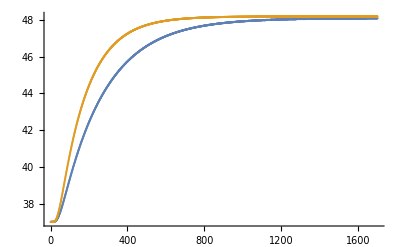

```mathematica
ListPlot[{actual,mesh[[108]]},PlotRange->All]
```